## Init

### Form factors

```mathematica
(* Formfactor definition and values from [1811.00983] *)
```

```mathematica
tplus[mK_]:=(mB+mK)^2;
tminus[mK_]:=(mB-mK)^2;
tzero[mK_]:=tplus[mK](1-Sqrt[1-tminus[mK]/tplus[mK]]);
```

```mathematica
zz[t_,mK_]:=(Sqrt[tplus[mK]-t]-Sqrt[tplus[mK]-tzero[mK]])/(Sqrt[tplus[mK]-t]+Sqrt[tplus[mK]-tzero[mK]]);
```

```mathematica
FF[q.b2_,x_,mK_]:=1/(1-(q.b2)/Subscript[m, R,x]^2)Sum[Subscript[α, k,x](zz[q.b2,mK]-zz[0,mK])^k,{k,0,2}]/.formFactors/.values/.masses/.couplings/.ckms;
```

```mathematica
V0AB[q.b2_,F0_,aAB_,bAB_]:= F0/(1-aAB (q.b2)/mB^2+bAB((q.b2)/mB^2)^2)/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
(* we need f0 and f+ only for the B->K pseudoscalar decay, but A0 for B->K^* vector decays for different K^* masses, so we explicitly have to add mP (or mK^*) here *)
```

```mathematica
(* all masses (and mass-dimension quantities) in GeV units *)
```

```mathematica
constants = {GevToInverseSec :> 1.5 10^24};
values={Subscript[α, 0,fzero]:>0.329, Subscript[α, 1,fzero]:>0.195,Subscript[α, 2,fzero]:>-0.446,Subscript[α, 0,fplus]:>0.329,Subscript[α, 1,fplus]:>-0.876,Subscript[α, 2,fplus]:>0.006,Subscript[α, 0,Azero]:>0.343,Subscript[α, 1,Azero]:>-1.130,Subscript[α, 2,Azero]:>2.326,Subscript[m, R,fzero]:>5.54 , Subscript[m, R,fplus]:>5.325 ,Subscript[m, R,Azero]:>5.279,F0BS700:>0.46, aS700:>1.6,bS700:>1.35 ,F0BS1430:>0.17, aS1430:>4.4,bS1430:>6.4 ,F0A:>0.22, F0B:>-0.45,aA:>2.4,aB:>1.34,bA:>1.78,bB:>0.69,ΘK1:>-34 Degree,mK1A:>1.31,mK1B:>1.34,V012700:>-0.52,V01400:>-0.07};
```

```mathematica
V0BK1270func[q.b2_]:=1/1.270(Sin[ΘK1] mK1A V0AB[q.b2,F0A,aA,bA]+Cos[ΘK1] mK1B V0AB[q.b2,F0B,aB,bB])/.values
V0BK1400func[q.b2_]:=1/1.4(Cos[ΘK1] mK1A V0AB[q.b2,F0A,aA,bA]-Sin[ΘK1] mK1B V0AB[q.b2,F0B,aB,bB])/.values
```

```mathematica
formFactors={fplus[q.b2_,F0_,a_,b_]:> V0AB[q.b2,F0,a,b],V0BK1270[q.b2_]:>V0BK1270func[q.b2] ,V0BK1400[q.b2_]:>V0BK1400func[q.b2] , fzero[q.b2_]:> FF[q.b2,fzero,mK],Azero[qsqr_,mP_]:>FF[qsqr,Azero,mP]};
```

### Masses and couplings

```mathematica
τB=1.638;(*ps*)
ΓtotalB=6.582*10^-25/(10^-12 τB);(*GeV*)
cτB=3 10^10 10^-12 τB(*in cm*);
```

```mathematica
masses={MW:>80.38,mW:>80.38,MZ:>91.19,mZ:>91.19,v:>246,vev:>246,Γh:>0.013,MT:>173,mt:>173,MC:>1.28,mc:>1.28,MU:>0.0022,mu:>0.0022,MB:>4.18,mb:>4.18,MS:>0.095,ms:>0.095,MD:>0.0047,md:>0.0047,mτ:>1.777,mμ:>0.106,me:>0.000511,mBs:>5.367,mBd:>5.280,mB:>5.279,mD:>1.86,mK:>0.4937, mKstarV892:>0.892, mKstarV1410:>1.41, mKstarV1680:>1.72,mKAV1270:>1.27,mKAV1400:>1.4,mKstarS700:>0.7,mKstarS1430:>1.43,mπ:>0.14,fBs:>0.227,fBd:>0.188};
ckms={CKM[3,3]:>1,Vtb:>1,CKM[3,2]:>39.4/1000,Vts:>39.4/1000,CKM[3,1]:>8.1/1000, Vtd:> 8.1/1000,CKM[2,3]:>42.2/1000,Vcb:>42.2/1000,CKM[2,2]:>0.997,Vcs:>0.997,CKM[2,1]:>0.218,Vcd:>0.218,CKM[1,3]:>3.94/1000,Vub:>3.94/1000,CKM[1,2]:>0.2243,Vus:>0.2243,CKM[1,1]:>0.9742,Vud:>0.9742}; 
(* PDG values, but Vtb is there actually 1.019±0.025 which we reduce to an exact 1 here *)
couplings={EL:>Sqrt[4 π*7.297/1000],SW:>Sqrt[0.231],CW:>Sqrt[1-0.231],GF:>1.166*10^(-5),Subscript[α,em]:>7.297*10^-3,alphaem:>7.297*10^-3,alphas:>0.1181};
```

### Γϕ

```mathematica
SetDirectory[ NotebookDirectory[]];
```

```mathematica
datapointsππ=ReadList[File["current/rate_pipi.dat"],{Real,Real},WordSeparators->{"\t"},RecordSeparators->{"\n"}];
```

ReadList::noopen: Cannot open File[current/rate_pipi.dat].

```mathematica
datapointsππ={{0.28001323,5.17024*10^(-10)},{0.27784854,1.0525554*10^(-9)},{0.2877911,1.8218304*10^(-9)},{0.30592537,3.3623317*10^(-9)},{0.33365947,5.277515*10^(-9)},{0.3639078,8.283586*10^(-9)},{0.41079497,1.2181233*10^(-8)},{0.47179008,1.7907567*10^(-8)},{0.5560635,2.7178222*10^(-8)},{0.6442094,4.2615103*10^(-8)},{0.73974603,5.5053757*10^(-8)},{0.8280175,9.213942*10^(-8)},{0.8877805,1.6462049*10^(-7)},{0.9437583,3.1379568*10^(-7)},{0.97783643,7.033213*10^(-7)},{1.002676,3.6842826*10^(-7)},{1.036807,1.5896644*10^(-7)},{1.0629779,7.317836*10^(-8)},{1.108985,3.958082*10^(-8)},{1.1371115,2.0074902*10^(-8)},{1.1865596,1.27616815*10^(-8)},{1.2277195,9.23311*10^(-9)},{1.2817607,8.933028*10^(-9)},{1.3385478,1.08358424*10^(-8)},{1.3852515,9.2141486*10^(-9)},{1.47,4.38*10^(-9)},{1.5,2.5269602*10^(-9)},{1.5614661,4.1001567*10^(-9)},{1.6033295,6.6537464*10^(-9)},{1.6742321,7.566051*10^(-9)},{1.7473112,5.4732547*10^(-9)},{1.8077103,3.5941348*10^(-9)},{1.88713,3.25975*10^(-9)},{1.9999999,3.7056085*10^(-9)}};
```

```mathematica
Γϕππ=Interpolation[datapointsππ,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
datapointsKK=ReadList[File["current/rate_KK.dat"],{Real,Real},WordSeparators->{"\t"},RecordSeparators->{"\n"}];
```

ReadList::noopen: Cannot open File[current/rate_KK.dat].

```mathematica
datapointsKK={{0.992899,1.39798*10^(-7)},{1.07269,1.07816*10^(-7)},{1.13916,8.87269*10^(-8)},{1.25236,8.04012*10^(-8)},{1.31897,8.56912*10^(-8)},{1.45009,8.02007*10^(-8)},{1.58049,7.26857*10^(-8)}{1.69277,5.42831*10^(-8)},{1.81310,4.18707*10^(-8)},{1.99304,3.44371*10^(-8)}};
```

```mathematica
ΓϕKK=Interpolation[datapointsKK,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
alphaSValues={{1.03,0.49},{1.27,0.40},{1.55,0.34},{2.14,0.28},{3.48,0.23},{6.11,0.19}};
```

```mathematica
AlphaS=Interpolation[alphaSValues,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
Γϕχ[mϕ_,mχ_,ξ_,α_]:=1/(8 π mϕ^2) HeavisideTheta[mϕ-2 mχ] ξ^2 Cos[α]^2 (mϕ^2-4 mχ^2)^(3/2) (* dark fermion *)
Γϕf[mϕ_,α_,mf_]:=HeavisideTheta[mϕ-2 mf] ((mf/v)^2 Sin[α]^2 (mϕ^2-4 mf^2)^(3/2))/(8 π mϕ^2) (* lepton *)
ΓϕW[mϕ_,α_]:=HeavisideTheta[mϕ-2 MW] Sin[α]^2 ((EL)^2 (4 (CW)^4 Sqrt[mϕ^2-4 MW^2] (mϕ^4-4 mϕ^2 MW^2+12 MW^4)))/(64 π (CW)^4 mϕ^2 MW^2 (SW)^2) (* W-boson *)
ΓϕZ[mϕ_,α_]:=HeavisideTheta[mϕ-2 MZ] Sin[α]^2 ((EL)^2 (Sqrt[mϕ^2-4 MZ^2] (CW^4 mϕ^4-4 CW^2 mϕ^2 MW^2+12 MW^4)))/(64 π (CW)^4 mϕ^2 MW^2 (SW)^2) (* Z-boson*)
Γϕγ[MH_,α_]:=Sin[α]^2 (EL^6*(MH^4*(3*MH^2-16*MT^2+18*MW^2)^2+256*MT^4*(MH^2-4*MT^2)^2*ArcTanh[MH/Sqrt[MH^2-4*MT^2]]^4-72*MH^2*MW^2*(MH^2-2*MW^2)*(3*MH^2-16*MT^2+18*MW^2)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^2+81*MW^4*(17*MH^4-64*MH^2*MW^2+64*MW^4)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^4+32*MT^2*(MH^2-4*MT^2)*ArcTanh[MH/Sqrt[MH^2-4*MT^2]]^2*(MH^2*(3*MH^2-16*MT^2+18*MW^2)-36*MW^2*(MH^2-2*MW^2)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^2)))/(18432*MH^5*MW^2*Pi^5*SW^2) (* Photon *)
Γϕg[mϕ_,α_]:=(Sin[α]^2alphas^2mϕ^3)/(32π^3 v^2) Abs[Sum[((mϕ^2/(4mq^2))+((mϕ^2/(4mq^2))-1)*(HeavisideTheta[(mϕ^2/(4mq^2))-1]*(-1/4) (Log[(1+Sqrt[1-1/(mϕ^2/(4mq^2))])/(1-Sqrt[1-1/(mϕ^2/(4mq^2))])]-I π)^2+HeavisideTheta[-(mϕ^2/(4mq^2))+1]ArcSin[Sqrt[(mϕ^2/(4mq^2))]]^2))/((mϕ^2/(4mq^2))^2),{mq,{mu,md,ms,mc,mb,mt}}]]^2*HeavisideTheta[mϕ-2](* gluons *)
Γϕπ[mϕ_,α_]:= Γϕππ[mϕ]*Sin[α]^2*HeavisideTheta[mϕ-2mπ/.masses]*HeavisideTheta[2-mϕ] (* pion *)
ΓϕK[mϕ_,α_]:= ΓϕKK[mϕ]*Sin[α]^2*HeavisideTheta[mϕ-2mK/.masses]*HeavisideTheta[2-mϕ] (* kaon *)
Γϕs[mϕ_,α_]:=3*HeavisideTheta[mϕ-2 mK] ((ms/v)^2 Sin[α]^2 (mϕ^2-4 mK^2)^(3/2))/(8 π mϕ^2)*HeavisideTheta[mϕ-2] (* strange quarks *)
Γϕc[mϕ_,α_]:=3*HeavisideTheta[mϕ-2 mD] ((mc/v)^2 Sin[α]^2 (mϕ^2-4 mD^2)^(3/2))/(8 π mϕ^2)*HeavisideTheta[mϕ-2] (* charm quarks *)
Γϕb[mϕ_,α_]:=3*HeavisideTheta[mϕ-2 mB] ((mb/v)^2 Sin[α]^2 (mϕ^2-4 mB^2)^(3/2))/(8 π mϕ^2)*HeavisideTheta[mϕ-2] (* bottom quarks *)
Γϕmoreπs[mϕ_,α_]:=5.1*10^(-9) Sin[α]^2 mϕ^2 Sqrt[mϕ^2-4mπ^2]*HeavisideTheta[mϕ-4mπ]*HeavisideTheta[2-mϕ] (* additional meson contributions *)
Γϕ[mϕ_,mχ_,ξ_,α_]:=(Γϕχ[mϕ,mχ,ξ,α]+Γϕf[mϕ,α,me]+Γϕf[mϕ,α,mμ]+Γϕf[mϕ,α,mτ]+Γϕπ[mϕ,α]+ΓϕK[mϕ,α]+Γϕmoreπs[mϕ,α]+Γϕg[mϕ,α]+Γϕs[mϕ,α]+Γϕc[mϕ,α]+Γϕb[mϕ,α]+Γϕγ[mϕ,α]+ΓϕW[mϕ,α]+ΓϕZ[mϕ,α])/.{alphas:>AlphaS[mϕ]}/.masses/.couplings
ΓϕSM[mϕ_,α_]:=Γϕ[mϕ,mϕ,0,α]/.HeavisideTheta[0]:>1
ΓϕBRDM[mϕ_,α_,BRχ_]:=ΓϕSM[mϕ,α](1+BRχ/(1-BRχ))(*ΓSM+Γχ for given BRχ*)
τϕ[mϕ_,mχ_,ξ_,α_]:=10^12(Γϕ[mϕ,mχ,ξ,α] GevToInverseSec)^-1/.constants (*in psc*)
τϕBRDM[mϕ_,α_,BRχ_]:=10^12(ΓϕBRDM[mϕ,α,BRχ] GevToInverseSec)^-1/.constants (*in psc*)
cτϕBRDM[mϕ_,α_,BRχ_]:=3 10^10 10^-12 τϕBRDM[mϕ,α,BRχ](*in cm*)
cτϕVisible[mϕ_,α_]:=3 10^10(ΓϕSM[mϕ,α] GevToInverseSec)^-1/.constants (*in psc*)
Γϕtoμμ[mϕ_,α_]:=HeavisideTheta[mϕ-2 mμ] ((mμ/v)^2 Sin[α]^2 (mϕ^2-4 mμ^2)^(3/2))/(8 π mϕ^2)
Γϕtoττ[mϕ_,α_]:=Γϕf[mϕ,α,mτ]
cτS[mS_,α_]:=Quiet[cτϕBRDM[mS,α,0]]
```

## Geometrical integration over detector

### Auxiliary

```mathematica
Eptransl={ES:>(mB^2+mS^2-mK^2)/(2mB),pS:>Sqrt[ES^2-mS^2]};
```

```mathematica
BIIparams={dres:>0.05,γB:>1.04,γβB:>0.28,NBBBelleII:>5*10^10}; 
ECLparams={ρmax:>146,zmin:>-125,zmax:>224};
(*CDCparams={ρmax:>113,zmin:>-65,zmax:>150};*)
CDCparams={ρmax:>113,zmin:>-125,zmax:>224};
```

```mathematica
λfunc[a_,b_,c_]=Sqrt[a^2+b^2+c^2-2a b-2b c-2c a];
```

### Norm

```mathematica
normIntd[ρ_,θ0_,mSp_,α_]=ρ^2 (γB+γβB ES/pS Cos[θ0])/Sin[θ0]^2 Exp[-(ρ mS)/(cτS pS Sin[θ0])]//.Eptransl(*/.BIIparams/.masses*)/.{mS:>mSp};
```

```mathematica
normcheck[mS_,α_]=(*-2π*) Integrate[normIntd[ρ,θ0,mS,α],{ρ,0,Infinity},{θ0,0,π}]
```

ConditionalExpression[((mB^2+((mK^2-mS^2)^2)/mB^2-2 (mK^2+mS^2))^(3/2) γB Abs[cτS]^3)/(2 Abs[mS]^3),mS/(cτS √(mB^2+((mK^2-mS^2)^2)/mB^2-2 (mK^2+mS^2)))∈ℝ&&cτS mS √(mB^2+((mK^2-mS^2)^2)/mB^2-2 (mK^2+mS^2))>0]

```mathematica
norm[mS_,α_]=(*-2π*) γB/2( (cτS[mS,α]λfunc[mB^2,mK^2,mS^2])/(mB mS))^3/.masses/.BIIparams;
```

InterpolatingFunction::dmval: Input value {0.212093} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

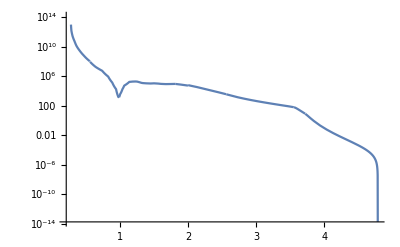

```mathematica
LogPlot[norm[mS,0.0001],{mS,2mμ/.masses,mB-mK/.masses}]
```

### Angles

```mathematica
dθoversinsqrθbydθ0[θ0_,mSp_]=(γB+γβB ES/pS Cos[θ0])/Sin[θ0]^2//.Eptransl/.mS:>mSp
```

(γB+((mB^2-mK^2+mSp^2) γβB Cos[θ0])/(2 mB √(-mSp^2+((mB^2-mK^2+mSp^2)^2)/(4 mB^2)))) Csc[θ0]^2

```mathematica
Cotθ[θ0_,mS_]=(γβB ES+γB pS Cos[θ0])/(pS Sin[θ0])//.Eptransl//Simplify
```

γB Cot[θ0]+((mB^2-mK^2+mS^2) γβB Csc[θ0])/(mB √(mB^2+((mK^2-mS^2)^2)/mB^2-2 (mK^2+mS^2)))

```mathematica
Sinθ[θ0_,mS_]=(pS Sin[θ0])/Sqrt[pS^2Sin[θ0]^2+(γβB ES+γB Cos[θ0]pS)^2]//.Eptransl//Simplify
```

(√(-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) Sin[θ0])/(√((((mB^2-mK^2+mS^2) γβB)/(2 mB)+√(-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) γB Cos[θ0])^2+(-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) Sin[θ0]^2))

```mathematica
θcutoff[mSp_]:=θ/.Solve[(pS^2 γB^2-ES^2 γβB^2+pS^2 Cot[θ]^2//.Eptransl/.BIIparams/.masses/.mS:>mSp)==0,{θ}]
θmax[mS_]:=Quiet[Max[Min[Select[θcutoff[mS],(Head[#]===Real&&#>0&&#<π/2)&],150°],17°]]
```

```mathematica
θ0min[mSp_]:=(tmin=ArcTan[-ES pS γB γβB+√(pS^2 Cot[θ]^2 (pS^2 γB^2-ES^2 γβB^2+pS^2 Cot[θ]^2)),ES pS γβB Cot[θ]+γB √(pS^2 Cot[θ]^2 (pS^2 γB^2-ES^2 γβB^2+pS^2 Cot[θ]^2)) Tan[θ]]//.Eptransl/.BIIparams/.masses/.mS:>mSp/.θ:>17°;If[Head[tmin]===Complex,0,tmin])
```

```mathematica
θ0max[mSp_]:=(tmax=ArcTan[-ES pS γB γβB-√(pS^2 Cot[θ]^2 (pS^2 γB^2-ES^2 γβB^2+pS^2 Cot[θ]^2)),ES pS γβB Cot[θ]-γB √(pS^2 Cot[θ]^2 (pS^2 γB^2-ES^2 γβB^2+pS^2 Cot[θ]^2)) Tan[θ]]//.Eptransl/.BIIparams/.masses/.mS:>mSp/.{θ:>If[θmax[mSp]==150°,150°,17°]};If[Head[tmax]===Complex,0,tmax])
```

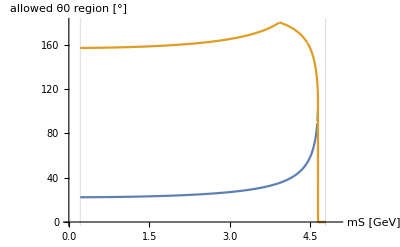

```mathematica
Plot[{θ0min[mS]/°,θ0max[mS]/°},{mS,2mμ/.masses,mB-mK/.masses},AxesLabel->{"mS [GeV]","allowed θ0 region [°]"},PlotRange->{{0,5},{0,180}},GridLines->{{2mμ/.masses,mB-mK/.masses},{}}]
```

### Integral proper

```mathematica
Integrate[ρ^2Exp[- a ρ] HeavisideTheta[ρ b-zmin] HeavisideTheta[-b ρ + zmax],{ρ,ρmin,ρmax}]
```

ConditionalExpression[(Piecewise[{{-(ⅇ^(-a ρmax) (2+2 a ρmax+a^2 ρmax^2))/a^3, b ρmax≤zmax&&b ρmax≥zmin}, {0, True}}])-(Piecewise[{{-(ⅇ^(-a ρmin) (2+2 a ρmin+a^2 ρmin^2))/a^3, b ρmin≤zmax&&b ρmin≥zmin}, {0, True}}]),((zmax-b ρmin)/(b ρmax-b ρmin)∉ℝ||Re[(zmax-b ρmin)/(b ρmax-b ρmin)]<0||Re[(zmax-b ρmin)/(b ρmax-b ρmin)]>1)&&((zmin-b ρmin)/(b ρmax-b ρmin)∉ℝ||Re[(zmin-b ρmin)/(b ρmax-b ρmin)]<0||Re[(zmin-b ρmin)/(b ρmax-b ρmin)]>1)&&((zmax-b ρmin)/(b ρmax-b ρmin)∉ℝ||(zmin-b ρmin)/(b ρmax-b ρmin)∉ℝ||Re[(zmax-b ρmin)/(b ρmax-b ρmin)]≥1||Re[(zmax-b ρmin)/(b ρmax-b ρmin)]≤0)]

```mathematica
ρintt[θ0_,mSp_,α_]=(-Exp[-a ρmax] (a^2ρmax^2+2a ρmax+2)/a^3 HeavisideTheta[-b ρmax + zmax]HeavisideTheta[b ρmax-zmin] +Exp[-a ρmin](a^2ρmin^2+2a ρmin+2)/a^3 HeavisideTheta[ b ρmin-zmin]HeavisideTheta[zmax-b ρmin])/.{a:>mS/(cτS[mS,α] pS Sin[θ0]),b:>Cotθ[θ0,mS],ρmin:>dres Sinθ[θ0,mS]}//.Eptransl/.mS:>mSp//PowerExpand;
```

```mathematica
θ0intdECL[θ0_,mSp_,α_]=dθoversinsqrθbydθ0[θ0,mSp]ρintt[θ0,mSp,α]//.Eptransl/.mS:>mSp/.BIIparams/.masses/.ECLparams;
```

```mathematica
θ0intdCDC[θ0_,mSp_,α_]=dθoversinsqrθbydθ0[θ0,mSp]ρintt[θ0,mSp,α]//.Eptransl/.mS:>mSp/.BIIparams/.masses/.CDCparams;
```

```mathematica
geoIntECL[mS_,α_]:=(*-2π*)NIntegrate[θ0intdECL[θ0,mS,α],{θ0,θ0min[mS],θ0max[mS]}]/norm[mS,α]
```

```mathematica
geoIntCDC[mS_,α_]:=(*-2π*)NIntegrate[θ0intdCDC[θ0,mS,α],{θ0,θ0min[mS],θ0max[mS]}]/norm[mS,α]
```

#### WIP

```mathematica
tmpρinttfh[θ0_,mSp_,α_]=Exp[-a ρmin](a^2ρmin^2+2a ρmin+2)/a^3 HeavisideTheta[ b ρmin-zmin]HeavisideTheta[zmax-b ρmin]/.{a:>mS/(cτS[mS,α] pS Sin[θ0]),b:>Cotθ[θ0,mS],ρmin:>dres Sinθ[θ0,mS]}//.Eptransl/.mS:>mSp//PowerExpand;
tmpρinttsh[θ0_,mSp_,α_]=Exp[-a ρmax] (a^2ρmax^2+2a ρmax+2)/a^3 HeavisideTheta[-b ρmax + zmax]HeavisideTheta[b ρmax-zmin] /.{a:>mS/(cτS[mS,α] pS Sin[θ0]),b:>Cotθ[θ0,mS],ρmin:>dres Sinθ[θ0,mS]}//.Eptransl/.mS:>mSp//PowerExpand;
tmpθ0intdCDCfh[θ0_,mSp_,α_]=(γB+γβB ES/pS Cos[θ0])/Sin[θ0]^2 tmpρinttfh[θ0,mSp,α]//.Eptransl/.mS:>mSp/.BIIparams/.masses/.CDCparams;
tmpθ0intdECLfh[θ0_,mSp_,α_]=(γB+γβB ES/pS Cos[θ0])/Sin[θ0]^2 tmpρinttfh[θ0,mSp,α]//.Eptransl/.mS:>mSp/.BIIparams/.masses/.ECLparams;
tmpθ0intdCDCsh[θ0_,mSp_,α_]=(γB+γβB ES/pS Cos[θ0])/Sin[θ0]^2 tmpρinttsh[θ0,mSp,α]//.Eptransl/.mS:>mSp/.BIIparams/.masses/.CDCparams;
tmpθ0intdECLsh[θ0_,mSp_,α_]=(γB+γβB ES/pS Cos[θ0])/Sin[θ0]^2 tmpρinttsh[θ0,mSp,α]//.Eptransl/.mS:>mSp/.BIIparams/.masses/.ECLparams;
tmpgeoIntECLfh[mS_,α_]:=(*-2π*)NIntegrate[tmpθ0intdECLfh[θ0,mS,α],{θ0,θ0min[mS],θ0max[mS]}]/norm[mS,α]
tmpgeoIntECLsh[mS_,α_]:=(*-2π*)NIntegrate[tmpθ0intdECLsh[θ0,mS,α],{θ0,θ0min[mS],θ0max[mS]}]/norm[mS,α]
tmpgeoIntECL[mS_,α_]:=tmpgeoIntECLfh[mS,α]-tmpgeoIntECLsh[mS,α]
```

```mathematica
(*θ0maxsh[mS_]=(θ0/.Solve[γβB ES+γB pS Cos[θ0]==zmax/ρmax pS Sin[θ0],{θ0}]//.Eptransl/.masses/.BIIparams/.ECLparams/.{C[1]:>0})[[2]];
θ0minsh[mS_]=(θ0/.Solve[γβB ES+γB pS Cos[θ0]==zmin/ρmax pS Sin[θ0],{θ0}]//.Eptransl/.masses/.BIIparams/.ECLparams/.{C[1]:>0})[[1]];*)
```

```mathematica
θ0maxsh[mS_]=(θ0/.Solve[γβB ES+γB pS Cos[θ0]==zmax/ρmax pS Sin[θ0],{θ0}]//.Eptransl/.masses/.BIIparams/.ECLparams/.{C[1]:>0});
θ0minsh[mS_]=(θ0/.Solve[γβB ES+γB pS Cos[θ0]==zmin/ρmax pS Sin[θ0],{θ0}]//.Eptransl/.masses/.BIIparams/.ECLparams/.{C[1]:>0});
```

```mathematica
θ0minsh[mS_]=θ0/.Solve[γβB ES+γB pS Cos[θ0]==zmin/ρmax pS Sin[θ0],{θ0}]//.Eptransl/.{C[1]:>0}
```

{ArcTan[(-((mB^2-mK^2+mS^2) √(-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) γB γβB ρmax^2)/(2 mB)-√((-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2))^2 zmin^4+(-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2))^2 zmin^2 γB^2 ρmax^2-((mB^2-mK^2+mS^2)^2 (-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) zmin^2 γβB^2 ρmax^2)/(4 mB^2)))/((-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) zmin^2+(-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) γB^2 ρmax^2),-1/(√(-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) zmin)(-((mB^2-mK^2+mS^2) γβB ρmax)/(2 mB)+((mB^2-mK^2+mS^2) (-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) γB^2 γβB ρmax^3)/(2 mB ((-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) zmin^2+(-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) γB^2 ρmax^2))+(√(-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) γB ρmax √((-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2))^2 zmin^4+(-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2))^2 zmin^2 γB^2 ρmax^2-((mB^2-mK^2+mS^2)^2 (-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) zmin^2 γβB^2 ρmax^2)/(4 mB^2)))/((-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) zmin^2+(-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) γB^2 ρmax^2))],ArcTan[(-((mB^2-mK^2+mS^2) √(-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) γB γβB ρmax^2)/(2 mB)+√((-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2))^2 zmin^4+(-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2))^2 zmin^2 γB^2 ρmax^2-((mB^2-mK^2+mS^2)^2 (-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) zmin^2 γβB^2 ρmax^2)/(4 mB^2)))/((-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) zmin^2+(-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) γB^2 ρmax^2),1/(√(-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) zmin)(((mB^2-mK^2+mS^2) γβB ρmax)/(2 mB)-((mB^2-mK^2+mS^2) (-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) γB^2 γβB ρmax^3)/(2 mB ((-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) zmin^2+(-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) γB^2 ρmax^2))+(√(-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) γB ρmax √(-(-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) zmin^2 (-(-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) zmin^2-(-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) γB^2 ρmax^2+((mB^2-mK^2+mS^2)^2 γβB^2 ρmax^2)/(4 mB^2))))/((-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) zmin^2+(-mS^2+((mB^2-mK^2+mS^2)^2)/(4 mB^2)) γB^2 ρmax^2))]}

```mathematica
Solve[θ0minsh[mS][[1]]==π,mS]
```

$Aborted

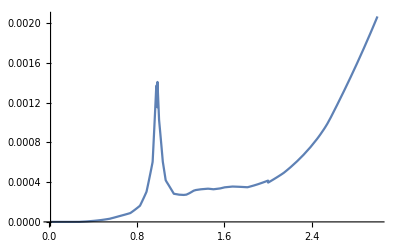

```mathematica
Plot[mS/(cτS[mS,α] pS Sin[θ0])//.Eptransl/.masses/.{α-> 10^-5,θ0-> π/2},{mS,0.01,3}]
```

```mathematica
Exp[-a ρmax] (a^2ρmax^2+2a ρmax+2)/a^3 HeavisideTheta[ b ρmin-zmin]HeavisideTheta[zmax-b ρmin] /.{a:>mS/(cτS[mS,α] pS Sin[θ0]),b:>Cotθ[θ0,mS],ρmin:>dres Sinθ[θ0,mS]}//.Eptransl/.BIIparams/.masses/.CDCparams/.{α-> 10^-3,θ0-> π/2,mS-> 1.4}
```

4.97198×10^-159+0. ⅈ

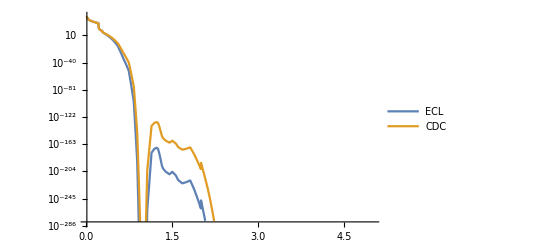

```mathematica
LogPlot[{(Exp[-a ρmax] (a^2ρmax^2+2a ρmax+2)/a^3 HeavisideTheta[ b ρmin-zmin]HeavisideTheta[zmax-b ρmin]/.{a:>mS/(cτS[mS,α] pS Sin[θ0]),b:>Cotθ[θ0,mS],ρmin:>dres Sinθ[θ0,mS]}//.Eptransl/.BIIparams/.masses/.ECLparams/.{α-> 10^-3,θ0-> π/2}),(Exp[-a ρmax] (a^2ρmax^2+2a ρmax+2)/a^3 HeavisideTheta[ b ρmin-zmin]HeavisideTheta[zmax-b ρmin] /.{a:>mS/(cτS[mS,α] pS Sin[θ0]),b:>Cotθ[θ0,mS],ρmin:>dres Sinθ[θ0,mS]}//.Eptransl/.BIIparams/.masses/.CDCparams/.{α-> 10^-3,θ0-> π/2})},{mS,0.01,5},PlotLegends->{"ECL","CDC"}]
```

InterpolatingFunction::dmval: Input value {2.4} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

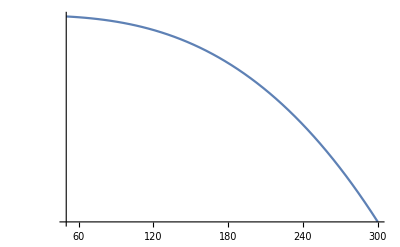

```mathematica
LogPlot[{Exp[-a ρmax] (a^2ρmax^2+2a ρmax+2)/a^3 HeavisideTheta[ b ρmin-zmin]HeavisideTheta[zmax-b ρmin]/.{a:>mS/(cτS[mS,α] pS Sin[θ0]),b:>Cotθ[θ0,mS],ρmin:>dres Sinθ[θ0,mS]}//.Eptransl/.BIIparams/.masses/.ECLparams/.{α-> 10^-5,θ0-> π/2,mS-> 2.4}},{ρmax,50,300}]
```

InterpolatingFunction::dmval: Input value {2.4} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

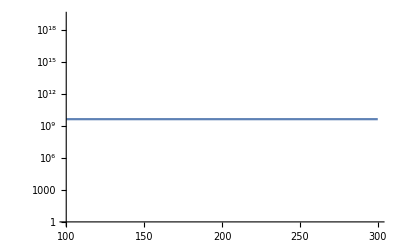

```mathematica
LogPlot[{Exp[-a ρmax] (a^2ρmax^2+2a ρmax+2)/a^3 HeavisideTheta[ b ρmin-zmin]HeavisideTheta[zmax-b ρmin]/.{a:>mS/(cτS[mS,α] pS Sin[θ0]),b:>Cotθ[θ0,mS],ρmin:>dres Sinθ[θ0,mS]}//.Eptransl/.BIIparams/.masses/.{α-> 10^-5,θ0-> π/2,mS-> 2.4,ρmax-> 100,zmin-> -125}},{zmax,100,300}]
```

InterpolatingFunction::dmval: Input value {2.4} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

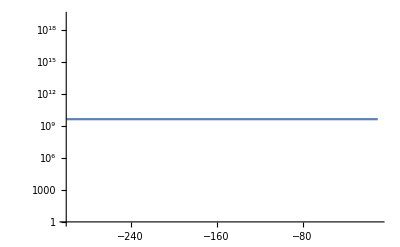

```mathematica
LogPlot[{Exp[-a ρmax] (a^2ρmax^2+2a ρmax+2)/a^3 HeavisideTheta[ b ρmin-zmin]HeavisideTheta[zmax-b ρmin]/.{a:>mS/(cτS[mS,α] pS Sin[θ0]),b:>Cotθ[θ0,mS],ρmin:>dres Sinθ[θ0,mS]}//.Eptransl/.BIIparams/.masses/.{α-> 10^-5,θ0-> π/2,mS-> 2.4,ρmax-> 100,zmax-> 200}},{zmin,-300,-10}]
```

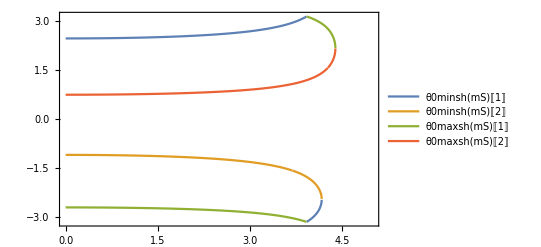

```mathematica
Plot[{θ0minsh[mS][[1]],θ0minsh[mS][[2]],θ0maxsh[mS][[1]],θ0maxsh[mS][[2]]},{mS,0,5},Frame->True,GridLines->{{}, {-π,π}},PlotLegends->"Expressions"]
```

### Plots

```mathematica
Manipulate[Plot[{θ0intdECL[θ0,mS,0.0001]},{θ0,θ0min[mS],θ0max[mS]},PlotRange->{{0,180°},All},GridLines->{{θ0min[mS],θ0max[mS]},{}}],{mS,2mμ/.masses,mB-mK/.masses}]
```

InterpolatingFunction::dmval: Input value {0.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.4} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Plot::plln: Limiting value θ0min[0.8] in {θ0,θ0min[0.8],θ0max[0.8]} is not a machine-sized real number.

```mathematica
Manipulate[Plot[{tmpθ0intdECLsh[θ0,mS,0.00001],tmpθ0intdCDCsh[θ0,mS,0.00001]},{θ0,θ0min[mS],θ0max[mS]},PlotRange->{{0,180°},All},GridLines->{{θ0min[mS],θ0max[mS]},{}},PlotLegends->{"ECL","CDC"}],{mS,2mμ/.masses,mB-mK/.masses}]
```

InterpolatingFunction::dmval: Input value {0.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.97} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.06} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Manipulate[Plot[{tmpθ0intdECLfh[θ0,mS,0.00001]-tmpθ0intdECLsh[θ0,mS,0.00001],tmpθ0intdCDCfh[θ0,mS,0.00001]-tmpθ0intdCDCsh[θ0,mS,0.00001]},{θ0,θ0min[mS],θ0max[mS]},PlotRange->{{0,180°},All},GridLines->{{θ0min[mS],θ0max[mS]},{}},PlotLegends->{"ECL","CDC"}],{mS,2mμ/.masses,mB-mK/.masses}]
```

InterpolatingFunction::dmval: Input value {0.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Manipulate[Plot[{tmpθ0intdECLfh[θ0,mS,0.0001]},{θ0,θ0min[mS],θ0max[mS]},PlotRange->{{0,180°},All},GridLines->{{θ0min[mS],θ0max[mS]},{}}],{mS,2mμ/.masses,mB-mK/.masses}]
```

InterpolatingFunction::dmval: Input value {0.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.79} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.38} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Plot::plln: Limiting value θ0min[0.212] in {θ0,θ0min[0.212],θ0max[0.212]} is not a machine-sized real number.

InterpolatingFunction::dmval: Input value {0.212093} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.47404}. NIntegrate obtained 4.2665×10^30+0. ⅈ and 6.00334×10^26 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.835075}. NIntegrate obtained 6.21238×10^30+0. ⅈ and 5.50101×10^27 for the integral and error estimates.

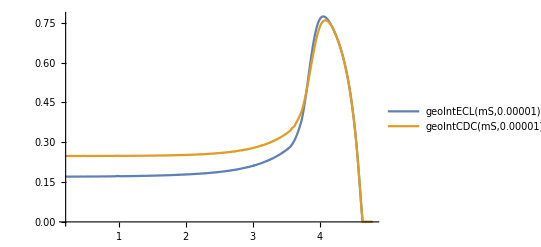

```mathematica
Plot[{geoIntECL[mS,0.00001],geoIntCDC[mS,0.00001]},{mS,2mμ/.masses,mB-mK/.masses}, PlotLegends->"Expressions"]
```

```mathematica
Manipulate[Plot[{tmpθ0intdECLfh[θ0,mS,0.0001]},{θ0,θ0min[mS],θ0max[mS]},PlotRange->{{0,180°},All},GridLines->{{θ0min[mS],θ0max[mS]},{}},PlotLabel-> "Only rmax differ"],{mS,2mμ/.masses,mB-mK/.masses}]
```

InterpolatingFunction::dmval: Input value {0.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

## B^+->K^(+(*)) branching ratios

### B^+ -> K^+pseudoscalar μμ,ππ,KK,ττ width

```mathematica
ΓBtoKPϕ[mϕ_,α_]:=Sin[α]^2(EL^6 MT^4 Vtb^2 (Conjugate[Vts])^2 fzero[mϕ^2]^2 (MB+MS)^2 √((mB^2-(mK-mϕ)^2)  (mB^2-(mK+mϕ)^2))((2 MT^2 mϕ^2 (MT^2-2 MW^2) (Log[MT^2]-Log[MW^2])+6 (MT^2-MW^2)^3-mϕ^2 (MT^4-4 MT^2 MW^2+3 MW^4))^2/ (MW^2-MT^2)^6))((mB^2-mK^2)^2)/(4194304 π^5 mB^3 MW^6 SW^6 (MB-MS)^2)HeavisideTheta[mB-(mK+mϕ)]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKPμμ[mϕ_,α_]:=ΓBtoKPϕ[mϕ,α]*Γϕtoμμ[mϕ,α]/ΓϕBRDM[mϕ,α,0]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKPττ[mϕ_,α_]:=ΓBtoKPϕ[mϕ,α]*Γϕtoττ[mϕ,α]/ΓϕBRDM[mϕ,α,0]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKPππ[mϕ_,α_]:=ΓBtoKPϕ[mϕ,α]*Γϕπ[mϕ,α]/ΓϕBRDM[mϕ,α,0]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKPKK[mϕ_,α_]:=ΓBtoKPϕ[mϕ,α]*ΓϕK[mϕ,α]/ΓϕBRDM[mϕ,α,0]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrBtoKPμμ[mϕ_,α_]:=ΓBtoKPμμ[mϕ,α]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

```mathematica
BrBtoKPττ[mϕ_,α_]:=ΓBtoKPττ[mϕ,α]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

```mathematica
BrBtoKPππ[mϕ_,α_]:=ΓBtoKPππ[mϕ,α]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

```mathematica
BrBtoKPKK[mϕ_,α_]:=ΓBtoKPKK[mϕ,α]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

#### SM contributions

```mathematica
BRBtoKμμSM=1.9 10^-6;
```

### B^+ -> K^*scalar μμ,ππ,KK,ττ width

```mathematica
ΓBtoKstarSϕGen[mϕ_,α_,mKscalar_,F0_,a_,b_]:=Sin[α]^2(EL^6 MT^4 Vtb^2 (Conjugate[Vts])^2 fplus[mϕ^2,F0,a,b]^2 (MB+MS)^2 √((mB^2-(mKscalar-mϕ)^2)  (mB^2-(mKscalar+mϕ)^2))1/((MW^2-MT^2)^6)(2 MT^2 mϕ^2 (MT^2-2 MW^2) (Log[MT^2]-Log[MW^2])+6 (MT^2-MW^2)^3-mϕ^2 (MT^4-4 MT^2 MW^2+3 MW^4))^2)((mB^2-mKscalar^2-mϕ^2)^2)/(4194304 π^5 mB^3 MW^6 SW^6 (MB+MS)^2)HeavisideTheta[mB-(mKscalar+mϕ)]

ΓBtoKstarSϕ[mϕ_,α_]:=(ΓBtoKstarSϕGen[mϕ,α,mKstarS700,F0BS700,aS700,bS700]+ΓBtoKstarSϕGen[mϕ,α,mKstarS1430,F0BS1430,aS1430,bS1430])/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKstarSμμ[mϕ_,α_]:=ΓBtoKstarSϕ[mϕ,α]*Γϕtoμμ[mϕ,α]/ΓϕBRDM[mϕ,α,0]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKstarSττ[mϕ_,α_]:=ΓBtoKstarSϕ[mϕ,α]*Γϕtoττ[mϕ,α]/ΓϕBRDM[mϕ,α,0]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKstarSππ[mϕ_,α_]:=ΓBtoKstarSϕ[mϕ,α]*Γϕπ[mϕ,α]/ΓϕBRDM[mϕ,α,0]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKstarSKK[mϕ_,α_]:=ΓBtoKstarSϕ[mϕ,α]*ΓϕK[mϕ,α]/ΓϕBRDM[mϕ,α,0]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrBtoKstarSμμ[mϕ_,α_]:=ΓBtoKstarSμμ[mϕ,α]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

```mathematica
BrBtoKstarSττ[mϕ_,α_]:=ΓBtoKstarSττ[mϕ,α]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

```mathematica
BrBtoKstarSππ[mϕ_,α_]:=ΓBtoKstarSππ[mϕ,α]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

```mathematica
BrBtoKstarSKK[mϕ_,α_]:=ΓBtoKstarSKK[mϕ,α]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms/.Belle2params;
```

#### SM contributions

```mathematica
BRBtoKμμSM=1.9 10^-6;
```

### B -> K^* vector μμ,ππ,KK,ττ width

```mathematica
ΓBtoKstarVϕGen[mϕ_,α_,mKstar_]:=Sin[α]^2(EL^6 MT^4 Vtb^2 (Conjugate[Vts])^2 Azero[mϕ^2,mKstar]^2 (MB+MS)^2 √((mB^2-(mKstar-mϕ)^2)  (mB^2-(mKstar+mϕ)^2))((2 MT^2 mϕ^2 (MT^2-2 MW^2) (Log[MT^2]-Log[MW^2])+6 (MT^2-MW^2)^3-mϕ^2 (MT^4-4 MT^2 MW^2+3 MW^4))^2/ (MW^2-MT^2)^6))((mB^2-(mKstar-mϕ)^2)  (mB^2-(mKstar+mϕ)^2))/(4194304 π^5 mB^3 MW^6 SW^6 (MB+MS)^2)HeavisideTheta[mB-(mKstar+mϕ)]/.formFactors/.values/.masses/.couplings/.ckms
ΓBtoKstarVϕ[mϕ_,α_]:=(ΓBtoKstarVϕGen[mϕ,α,mKstarV892]+ΓBtoKstarVϕGen[mϕ,α,mKstarV1410]+ΓBtoKstarVϕGen[mϕ,α,mKstarV1680])/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKstarVμμ[mϕ_,α_]:=ΓBtoKstarVϕ[mϕ,α]*Γϕtoμμ[mϕ,α]/ΓϕBRDM[mϕ,α,0]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKstarVττ[mϕ_,α_]:=ΓBtoKstarVϕ[mϕ,α]*Γϕtoττ[mϕ,α]/ΓϕBRDM[mϕ,α,0]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKstarVππ[mϕ_,α_]:=ΓBtoKstarVϕ[mϕ,α]*Γϕπ[mϕ,α]/ΓϕBRDM[mϕ,α,0]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKstarVKK[mϕ_,α_]:=ΓBtoKstarVϕ[mϕ,α]*ΓϕK[mϕ,α]/ΓϕBRDM[mϕ,α,0]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrBtoKstarVμμ[mϕ_,α_]=ΓBtoKstarVμμ[mϕ,α]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms;
```

```mathematica
BrBtoKstarVττ[mϕ_,α_]=ΓBtoKstarVττ[mϕ,α]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms;
```

```mathematica
BrBtoKstarVππ[mϕ_,α_]=ΓBtoKstarVππ[mϕ,α]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms;
```

```mathematica
BrBtoKstarVKK[mϕ_,α_]=ΓBtoKstarVKK[mϕ,α]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms;
```

#### SM contributions

### B -> K axialvector μμ,ππ,KK,ττ width

```mathematica
ΓBtoKAVϕGen[mϕ_,α_,mKstar_]:=Sin[α]^2(EL^6 MT^4 Vtb^2 (Conjugate[Vts])^2 V0[mϕ^2]^2 (MB+MS)^2 √((mB^2-(mKstar-mϕ)^2)  (mB^2-(mKstar+mϕ)^2))1/((MW^2-MT^2)^6)(2 MT^2 mϕ^2 (MT^2-2 MW^2) (Log[MT^2]-Log[MW^2])+6 (MT^2-MW^2)^3-mϕ^2 (MT^4-4 MT^2 MW^2+3 MW^4))^2)((mB^2-(mKstar-mϕ)^2)  (mB^2-(mKstar+mϕ)^2))/(4194304 π^5 mB^3 MW^6 SW^6 (MB-MS)^2)HeavisideTheta[mB-(mKstar+mϕ)]
ΓBtoKstarAVϕ[mϕ_,α_]:=((ΓBtoKAVϕGen[mϕ,α,mKAV1270]/.V0-> V0BK1270)+(ΓBtoKAVϕGen[mϕ,α,mKAV1400]/.V0-> V0BK1400))/.formFactors/.values/.masses/.couplings/.ckms;
```

```mathematica
ΓBtoKAVμμ[mϕ_,α_]:=ΓBtoKstarAVϕ[mϕ,α]*Γϕtoμμ[mϕ,α]/ΓϕBRDM[mϕ,α,0]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKAVττ[mϕ_,α_]:=ΓBtoKstarAVϕ[mϕ,α]*Γϕtoττ[mϕ,α]/ΓϕBRDM[mϕ,α,0]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKAVππ[mϕ_,α_]:=ΓBtoKstarAVϕ[mϕ,α]*Γϕπ[mϕ,α]/ΓϕBRDM[mϕ,α,0]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
ΓBtoKAVKK[mϕ_,α_]:=ΓBtoKstarAVϕ[mϕ,α]*ΓϕK[mϕ,α]/ΓϕBRDM[mϕ,α,0]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrBtoKAVμμ[mϕ_,α_]=ΓBtoKAVμμ[mϕ,α]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms;
```

```mathematica
BrBtoKAVττ[mϕ_,α_]=ΓBtoKAVττ[mϕ,α]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms;
```

```mathematica
BrBtoKAVππ[mϕ_,α_]=ΓBtoKAVππ[mϕ,α]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms;
```

```mathematica
BrBtoKAVKK[mϕ_,α_]=ΓBtoKAVKK[mϕ,α]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms;
```

#### SM contributions

### Sum over all K’s

```mathematica
BrBtoKμμ[mS_,α_]:=BrBtoKAVμμ[mS,α]+BrBtoKstarVμμ[mS,α]+BrBtoKstarSμμ[mS,α]+BrBtoKPμμ[mS,α]
```

```mathematica
BrBtoKππ[mS_,α_]:=BrBtoKAVππ[mS,α]+BrBtoKstarVππ[mS,α]+BrBtoKstarSππ[mS,α]+BrBtoKPππ[mS,α]
```

```mathematica
BrBtoKKK[mS_,α_]:=BrBtoKAVKK[mS,α]+BrBtoKstarVKK[mS,α]+BrBtoKstarSKK[mS,α]+BrBtoKPKK[mS,α]
```

```mathematica
BrBtoKττ[mS_,α_]:=BrBtoKAVττ[mS,α]+BrBtoKstarVττ[mS,α]+BrBtoKstarSττ[mS,α]+BrBtoKPττ[mS,α]
```

### Plots and Checks

InterpolatingFunction::dmval: Input value {0.300086} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

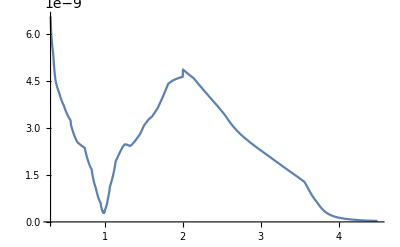

```mathematica
Plot[BrBtoKμμ[mS,0.0001],{mS,0.3,4.5}]
```

## Numbers of decays within detector

### Definitions

```mathematica
NμμECL[mS_,α_]:=1.93NBBBelleII  BrBtoKμμ[mS,α] geoIntECL[mS,α]/.formFactors/.values/.masses/.couplings/.ckms/.BIIparams
```

```mathematica
NππECL[mS_,α_]:=1.93NBBBelleII BrBtoKππ[mS,α]geoIntECL[mS,α]/.formFactors/.values/.masses/.couplings/.ckms/.BIIparams
```

```mathematica
NKKECL[mS_,α_]:=1.93NBBBelleII  BrBtoKKK[mS,α] geoIntECL[mS,α]/.formFactors/.values/.masses/.couplings/.ckms/.BIIparams
```

```mathematica
NττECL[mS_,α_]:=1.93NBBBelleII BrBtoKττ[mS,α]geoIntECL[mS,α]/.formFactors/.values/.masses/.couplings/.ckms/.BIIparams
```

```mathematica
NμμCDC[mS_,α_]:=1.93NBBBelleII  BrBtoKμμ[mS,α] geoIntCDC[mS,α]/.formFactors/.values/.masses/.couplings/.ckms/.BIIparams
```

```mathematica
NππCDC[mS_,α_]:=1.93NBBBelleII BrBtoKππ[mS,α]geoIntCDC[mS,α]/.formFactors/.values/.masses/.couplings/.ckms/.BIIparams
```

```mathematica
NKKCDC[mS_,α_]:=1.93NBBBelleII  BrBtoKKK[mS,α] geoIntCDC[mS,α]/.formFactors/.values/.masses/.couplings/.ckms/.BIIparams
```

```mathematica
NττCDC[mS_,α_]:=1.93NBBBelleII BrBtoKττ[mS,α]geoIntCDC[mS,α]/.formFactors/.values/.masses/.couplings/.ckms/.BIIparams
```

### mS-NXX-Plots

#### Definitions

```mathematica
mSNμμplotECL[α_]:=Plot[NμμECL[mS,α],{mS,2mμ/.masses,(mB-mK)/.masses},AxesLabel->{"m_S [GeV]","N_μμ"},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,16]]
```

```mathematica
mSNππplotECL[α_]:=Plot[NππECL[mS,α],{mS,2mμ/.masses,(mB-mK)/.masses},AxesLabel->{"m_S [GeV]","N_ππ"},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,16]]
```

```mathematica
mSNKKplotECL[α_]:=Plot[NKKECL[mS,α],{mS,2mμ/.masses,(mB-mK)/.masses},AxesLabel->{"m_S [GeV]","N_KK"},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,16]]
```

```mathematica
mSNττplotECL[α_]:=Plot[NττECL[mS,α],{mS,2mμ/.masses,(mB-mK)/.masses},AxesLabel->{"m_S [GeV]","N_ττ"},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,16]]
```

```mathematica
mSNμμplotCDC[α_]:=Plot[NμμCDC[mS,α],{mS,2mμ/.masses,(mB-mK)/.masses},AxesLabel->{"m_S [GeV]","N_μμ"},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,16]]
```

```mathematica
mSNππplotCDC[α_]:=Plot[NππCDC[mS,α],{mS,2mμ/.masses,(mB-mK)/.masses},AxesLabel->{"m_S [GeV]","N_ππ"},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,16]]
```

```mathematica
mSNKKplotCDC[α_]:=Plot[NKKCDC[mS,α],{mS,2mμ/.masses,(mB-mK)/.masses},AxesLabel->{"m_S [GeV]","N_KK"},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,16]]
```

```mathematica
mSNττplotCDC[α_]:=Plot[NττCDC[mS,α],{mS,2mμ/.masses,(mB-mK)/.masses},AxesLabel->{"m_S [GeV]","N_ττ"},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,16]]
```

#### Plots

InterpolatingFunction::dmval: Input value {0.212093} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.47404}. NIntegrate obtained 4.2665×10^24+0. ⅈ and 6.00334×10^20 for the integral and error estimates.

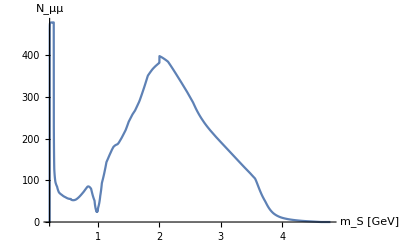

```mathematica
mSNμμplotECL[0.0001]
```

InterpolatingFunction::dmval: Input value {0.212093} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.835075}. NIntegrate obtained 6.21238×10^24+0. ⅈ and 5.50101×10^21 for the integral and error estimates.

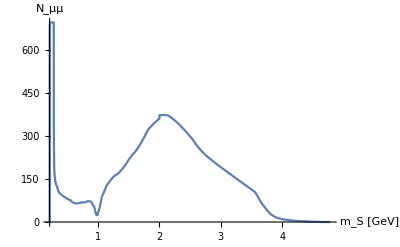

```mathematica
mSNμμplotCDC[0.0001]
```

### ContourPlots

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.47404}. NIntegrate obtained 2.21405×10^35+0. ⅈ and 3.11535×10^31 for the integral and error estimates.

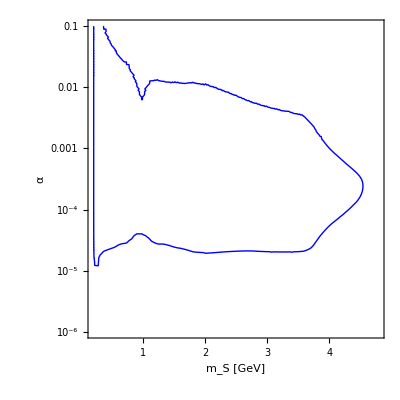

```mathematica
CPμμECL=ContourPlot[NμμECL[mS,α],{mS,2mμ/.masses,mB-mK/.masses},{α,10^-6,0.1},ScalingFunctions->{None,"Log"},FrameLabel->{"m_S [GeV]","α"},ContourShading->None,ContourStyle->{Blue},Contours->{3}]
```

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.835076}. NIntegrate obtained 3.22384×10^35+0. ⅈ and 2.85468×10^32 for the integral and error estimates.

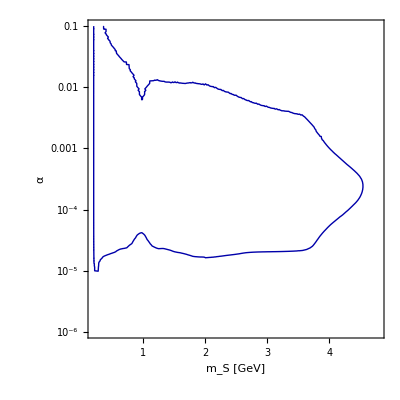

```mathematica
CPμμCDC=ContourPlot[NμμCDC[mS,α],{mS,2mμ/.masses,mB-mK/.masses},{α,10^-6,0.1},ScalingFunctions->{None,"Log"},FrameLabel->{"m_S [GeV]","α"},ContourShading->None,ContourStyle->{Darker[Blue]},Contours->{3}]
```

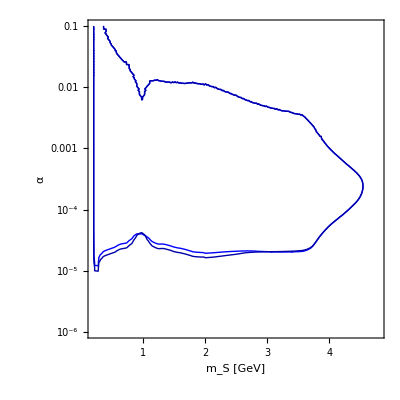

```mathematica
Show[Out[411],Out[474]]
```

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.47404}. NIntegrate obtained 2.21405×10^35+0. ⅈ and 3.11535×10^31 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.47404}. NIntegrate obtained 2.21405×10^35+0. ⅈ and 3.11535×10^31 for the integral and error estimates.

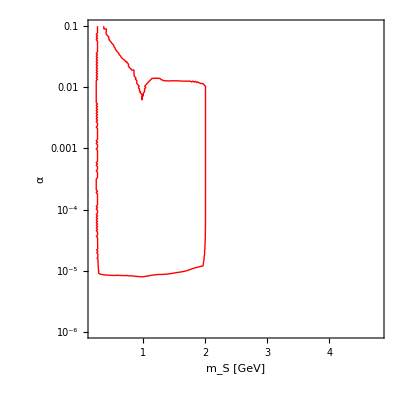

```mathematica
CPπKECL=ContourPlot[NππECL[mS,α]+NKKECL[mS,α],{mS,2mμ/.masses,mB-mK/.masses},{α,10^-6,0.1},ScalingFunctions->{None,"Log"},FrameLabel->{"m_S [GeV]","α"},ContourShading->None,ContourStyle->{Red},Contours->{3}]
```

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.835076}. NIntegrate obtained 3.22384×10^35+0. ⅈ and 2.85468×10^32 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.835076}. NIntegrate obtained 3.22384×10^35+0. ⅈ and 2.85468×10^32 for the integral and error estimates.

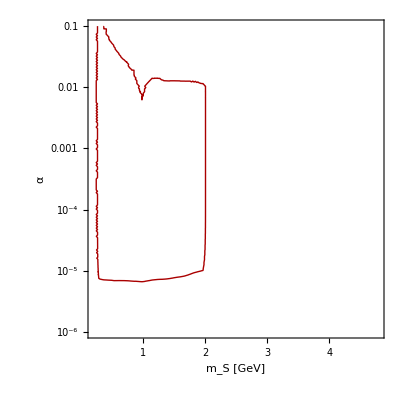

```mathematica
CPπKCDC=ContourPlot[NππCDC[mS,α]+NKKCDC[mS,α],{mS,2mμ/.masses,mB-mK/.masses},{α,10^-6,0.1},ScalingFunctions->{None,"Log"},FrameLabel->{"m_S [GeV]","α"},ContourShading->None,ContourStyle->{Darker[Red]},Contours->{3}]
```

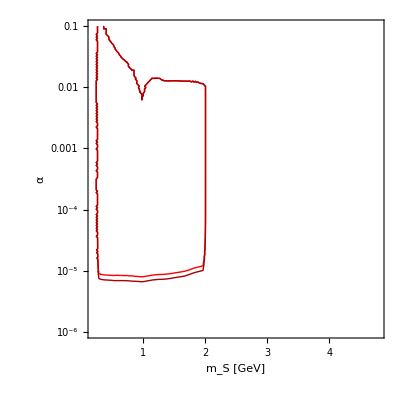

```mathematica
Show[Out[475],Out[476]]
```

```mathematica
CPττECL=ContourPlot[NττECL[mS,α],{mS,2mμ/.masses,mB-mK/.masses},{α,10^-6,0.1},ScalingFunctions->{None,"Log"},FrameLabel->{"m_S [GeV]","α"},ContourShading->None,ContourStyle->{Green},Contours->{3}]
```

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.47404}. NIntegrate obtained 2.21405×10^35+0. ⅈ and 3.11535×10^31 for the integral and error estimates.

-Graphics-

```mathematica
CPττCDC=ContourPlot[NττCDC[mS,α],{mS,2mμ/.masses,mB-mK/.masses},{α,10^-6,0.1},ScalingFunctions->{None,"Log"},FrameLabel->{"m_S [GeV]","α"},ContourShading->None,ContourStyle->{Darker[Green]},Contours->{3}]
```

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.835076}. NIntegrate obtained 3.22384×10^35+0. ⅈ and 2.85468×10^32 for the integral and error estimates.

-Graphics-

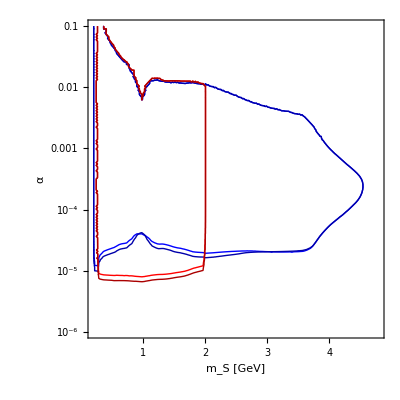

```mathematica
Show[Out[477],Out[478],Out[491],Out[492],AxesStyle->Directive[14,Black],LabelStyle->Directive[16,Black]]
```